Ryan Foundoulis
605107291
ryanfoundoulis@gmail.com
HW 4

```mathematica
(* Problem 1 *)
Remove["Global`*"]

(* Reality *)

SetAttributes[{m,L,g,ax}, Constant]
$Assumptions = 
	{ Element[{m,L,g,ax}, Reals] && m>0 && L > 0 && g > 0 && ax > 0};
debug = True;

(* Lagrangian *)

T = 1/2 m (x'[t]^2+y'[t]^2);
V = m g y[t];
lag = T - V;

(* Generalized Coords *)

x[t_] = 1/2 ax t^2 +L Sin[θ[t]];
y[t_] = - L Cos[θ[t]];

Print["Lagrangian = ", lag //Simplify]

(* EL Generator *)
EL[q_] := D[lag, q] - Dt[D[lag, D[q,t]], t] + Sum[λ[j][t] D[G[j],q], {j, 1, NCONST}] == 0 //Simplify;

(* Cement the EQ of Motion *)

eqnθ = EL[θ[t]];

(* Eq of motion *)

smallθ = Series[eqnθ, {θ[t],0,1}] //Normal;
soln = DSolve[{smallθ, θ[0]==θ0,θ'[0]==0}, θ[t], t][[1]];
θ[t_] = θ[t] /. soln;

Print["Equilibrium displacement: ", θ[t]]
Print["Frequency (seen by observer): ", Sqrt[g/L]]
```

Lagrangian = 1/2 m (ax^2 t^2+2 g L Cos[θ[t]]+2 ax L t Cos[θ[t]] θ'[t]+L^2 θ'[t]^2)

Equilibrium displacement: (-ax+ax Cos[√(g/L) t]+g θ0 Cos[√(g/L) t])/g

Frequency (seen by observer): √(g/L)

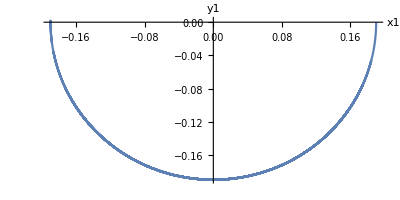

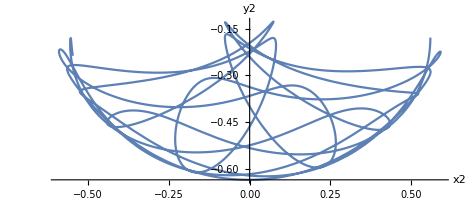

Lagrangian: 1/24 (12 g (L2 m2 Cos[α[t]]+L1 (m1+2 m2) Cos[θ[t]])+(12 L1^2+7 L2^2) m2 α'[t]^2+12 L1 L2 m2 Cos[α[t]-θ[t]] α'[t] θ'[t]+L1^2 (7 m1+12 m2) θ'[t]^2)

Lagrangian: 1/24 (12 g (L2 m2 Cos[α[t]]+L1 (m1+2 m2) Cos[θ[t]])+(12 L1^2+7 L2^2) m2 α'[t]^2+12 L1 L2 m2 Cos[α[t]-θ[t]] α'[t] θ'[t]+L1^2 (7 m1+12 m2) θ'[t]^2)

-Graphics-

-Graphics-

```mathematica
(* Problem 2 *)
Remove["Global`*"]

SetAttributes[{m1, m2, L1, L2, g}, Constant]

$Assumptions = 
	{ Element[{m1,L1,m2, L2, g}, Reals] && m1>0 && L1 > 0 && m2 > 0 && L2 > 0 && g > 0};
debug = true;

(* Lagrangian *)

T = 1/2 m1(x1'[t]^2+y1'[t]^2) + 1/2 m2(x2'[t]^2+y2'[t]^2) + 1/2 I1 θ'[t]^2+1/2 I2 α'[t]^2;
V = m1 g y1[t]+ m2 g y2[t];
lag = T - V;

(* Generalized coords *)

(* Coordinates accounting for Center of Mass *)
x1[t_]= (L1 Sin[θ[t]])/2;
y1[t_]= -(L1 Cos[θ[t]])/2;

x2[t_]=(L2 Sin[α[t]])/2 + L1 Sin[θ[t]];
y2[t_]=-(L2 Cos[α[t]])/2-L1 Cos[θ[t]] ;

I1 = 1/3 m1 L1^2;
I2 = 1/3 m2 L2^2 +m2 L1^2;

(* EL Generator *)
EL[q_] := D[lag, q] - Dt[D[lag, D[q,t]], t] + Sum[λ[j][t] D[G[j],q], {j, 1, NCONST}] == 0 //Simplify;

(* Cement the EQ of Motion *)
eqnθ = EL[θ[t]];
eqnα = EL[α[t]];

Print["Lagrangian: ", lag //FullSimplify]

(* Solve *)
ellist = {eqnθ,eqnα};
iclist={θ[0]==θ0,α[0] == α0, θ'[0]==0,α'[0]==0};
eqnlist=Join[ellist,iclist];

m1 = 1;
m2 = 2;
g = 10;
L1 = 15/(2π)^2;
L2 = 20/(2π)^2;
θ0 = π/2;
α0 = π/4;
tmin = 0;
tmax = 10;

soln = NDSolve[eqnlist, {θ,α},{t,tmin,tmax},MaxSteps->Infinity][[1]];
If[debug, Plot[θ[t]/.soln, {t, tmin, tmax}, AxesLabel-> {"t","θ"}]];
If[debug, Plot[α[t]/.soln, {t, tmin, tmax}, AxesLabel-> {"t","α"}]];

x1[t_]=x1[t]/.soln;
y1[t_]=y1[t]/.soln;
x2[t_]=x2[t]/.soln;
y2[t_]=y2[t]/.soln;

ParametricPlot[{x1[t], y1[t]}, {t,tmin,tmax},AxesLabel->{"x1","y1"}]
ParametricPlot[{x2[t], y2[t]}, {t,tmin,tmax},AxesLabel->{"x2","y2"}]
scale=0.0075;
range={{-1.2*(L1+L2)},{-1.2*(L1+L2)},(1/2)*(L1+L2)};

traj1[t_]:={Sin[θ[t]], -Cos[θ[t]]};
traj2[t_]:={Sin[θ[t]], -Cos[ϕ[t]]};

str1[t_]:=ListLinePlot[{{0,0},{x1[t],y1[t]}}/.soln];
b1[t_]:=Graphics[{PointSize[0.02], Point[{x1[t],y1[t]}/.soln]}];
str2[t_]:=ListLinePlot[{{x1[t]/.soln, y1[t]/.soln},{x2[t],y2[t]}}/.soln];
b2[t_]:=Graphics[{PointSize[0.02], Point[{x2[t],y2[t]}/.soln]}];
art[t_]:=Show[str1[t], str2[t],b1[t], b2[t], PlotRange-> range, PlostLabel -> "Double Physical Pendulum"]
Animate[art[t], {t, tmin, tmax}]
```

```mathematica
(* Problem 3 *)
Remove["Global`*"]

SetAttributes[{m,l,θ,g, r1, r2},Constant]

$Assumptions=
{Element[{θ,m,l,g},Reals] && m> 0 && g> 0 && l > 0 && θ>0&& r1> 0&& r2> 0};

moi=(1/2)*m*(r1^2+r2^2);

T=(1/2)*m*(x'[t]^2+y'[t]^2)+(1/2)moi*α'[t]^2;
V=m*g*y[t];
lag=T-V;

(* Generalized Coords *)

x[t_]=(l-r2*α[t])Cos[θ];
y[t_]=(r2*α[t]-l)Sin[θ];



alpha= D[lag, α[t]]-D[D[lag, α'[t]], t]==0//Simplify;
soln=DSolve[{alpha, α[0]==α0, α'[0]==0},α[t],t][[1]];


x[t_]=x[t]/.soln;
y[t_]=y[t]/.soln;
α[t_]=α[t]/.soln;

(* Prepare Graphics *)

range={{0,l}, {0, 3l/2}};
ramp=Graphics[Triangle[{{0, 0},{0,2.25},{3.75, 0}}]];


disk1[t_]:= Graphics[Circle[{x[t]-l Cos[θ]+r2 Cos[θ],y[t]+2l Sin[θ]+r2 Sin[θ]},r2]];
disk2[t_]:= Graphics[Circle[{x[t]-l Cos[θ]+r2 Cos[θ],y[t]+2l Sin[θ]+r2 Sin[θ]},r1]];

line=Graphics[{Yellow, Line[{{0,l Sin[θ]+ r2},{l Cos[θ],r2}}]}];
pix[t_]:=Show[ramp, disk1[t], disk2[t], line, Axes-> True,PlotRange->range];

l=5;
m=2;
g=5;
θ=30 Degree;
r1=1;
r2=2;
α0=0;
tlo=0;
thi=5;

Animate[pix[t],{t, tlo, thi}]
```